```mathematica
loss[x_,n_]=1/n(x-1)^n;
g[x_,n_]=D[loss[x,n],x];
update[x_,λ_,η_,p_,n_]:=Abs[x]^(2-p)/(Abs[x]^(2-p)+η λ)(x-η g[x,n])
```

```mathematica
exact[p_]:=Threshold[ParallelTable[{λ,x/.FindMinimum[loss[x,4]+λ/p Abs[x]^p,{x,0.4}][[2]]//Quiet},{λ,0,.8,.001}],10^-8];
```

```mathematica
GD[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,update[X[[-1]],λ,0.9,p,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,.8,.001}];
```

```mathematica
pp=0.7;
x0 list={GD[10^-4,pp],GD[10^-2,pp],GD[1,pp],exact[pp]};
```

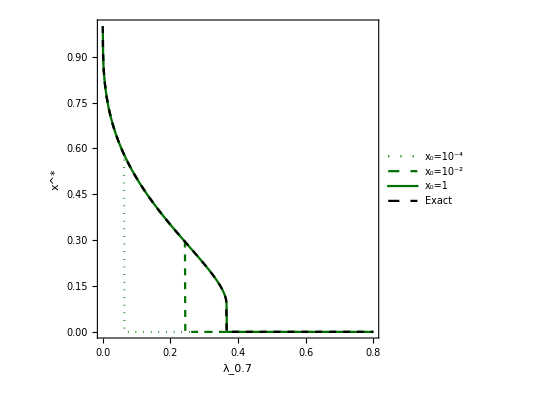

```mathematica
ListPlot[

x0 list,
Joined->True,
Frame->True,
AspectRatio->1,
PlotStyle->{{Green//Darker//Darker,Dotted},{Green//Darker//Darker,Dashed},{Green//Darker//Darker},{Dashed,Black}},

PlotLegends->Placed[{"x_0=10^-4","x_0=10^-2","x_0=1","Exact"},{Right,Top}],

FrameLabel->{"λ_0.7","x^*"},
FrameStyle->14
]
```

```mathematica
GD log[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,update[X[[-1]],λ,0.8,p,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,1,0.001}];

λc x0 list=Table[{x0,Select[GD log[x0,pp],#[[2]]==0&][[1,1]]},{x0,PowerRange[10.^-5,1,10^(5/50)]}];
fit[x_]=10^Fit[Select[λc x0 list,#[[1]]<10^-2&]//Log10,{1,x},x]/.x->Log10[x];
```

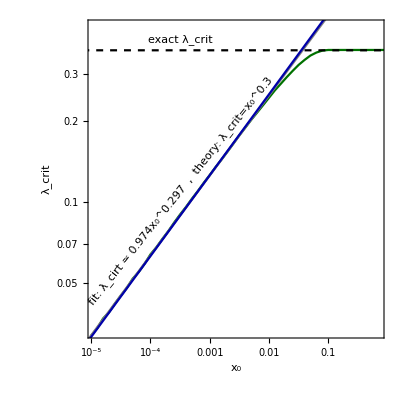

```mathematica
base=fit[1];
pow=D[Log[fit[x]/fit[1]],x]/.x->1;
formattedExpression=ToString[NumberForm[base,{∞,3}]]<>"\!\(\*SubsuperscriptBox[\(x\), \(0\), \("<>ToString[NumberForm[pow,{∞,3}]]<>"\)]\)";

Show[
ListLogLogPlot[λc x0 list,PlotStyle->{{Green//Darker//Darker}},Joined->True],
LogLogPlot[{fit[x],x^(1-pp),Select[x0 list[[-1]],#[[2]]==0&][[1,1]]},{x,10^-8,1},PlotStyle->{{Gray},Blue//Darker,{Black,Dashed}}],

Frame->True,
AspectRatio->1,
PlotRange->{{Log[1.1 10^-5],Log[0.7]},{Log[0.033],Log[0.45]}},
FrameStyle->14,
FrameLabel->{"x_0","λ_crit"},
Epilog->{
Inset[Style[Rotate["fit: λ_cirt ≃ "<>formattedExpression<>"  ,  theory: λ_crit=x_0^0.3",π/3.5]],{Log[10^-3.5],Log[.11]}],
Inset[Style["exact λ_crit"],{Log[10^-3.5],Log[0.4]}]
},

Background->White

]
```

```mathematica
D[Log[fit[x]/fit[1]],x]/.x->1
```

```mathematica
fit[x]
```

0.973995 x^0.296514

0.297

```mathematica
"x_0^0.34"
```

0.366

```mathematica
{"01:01:25",}
```

```mathematica
GD WU[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
If[i>3,AppendTo[X,update[X[[-1]],λ ,0.9,p,4]//Chop],AppendTo[X,update[X[[-1]],10^-8 λ ,0.9,p,4]//Chop]]
];
{λ,X[[-1]]},
{λ,0,.8,.001}];
```

```mathematica
pp=0.7;
x0 list={GD WU[10^-4,pp],GD WU[10^-2,pp],GD WU[1,pp],exact[pp]};
```

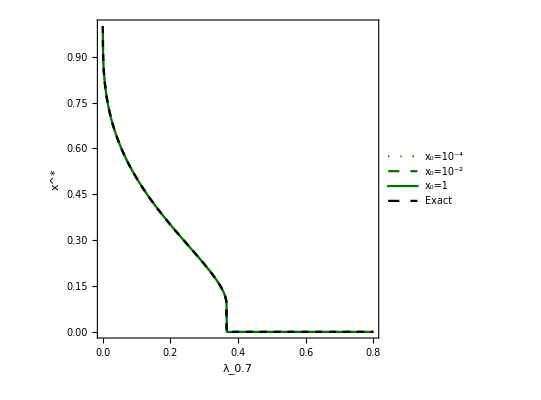

```mathematica
ListPlot[

x0 list,
Joined->True,
Frame->True,
AspectRatio->1,
PlotStyle->{{Green//Darker//Darker,Dotted},{Green//Darker//Darker,Dashed},{Green//Darker//Darker},{Dashed,Black}},

PlotLegends->Placed[{"x_0=10^-4","x_0=10^-2","x_0=1","Exact"},{Right,Top}],

FrameLabel->{"λ_0.7","x^*"},
FrameStyle->14
]
```

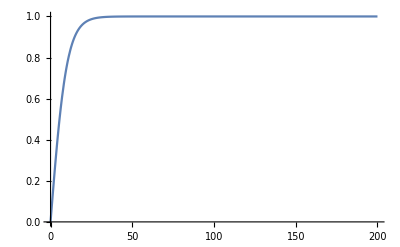

```mathematica
Plot[Tanh[x/10],{x,0,200},PlotRange->All]
```

```mathematica
loss[x_,n_]=1/n(x-1)^n;
g[x_,n_]=D[loss[x,n],x];
update[x_,λ_,η_,p_,n_]:=Abs[x]^(2-p)/(Abs[x]^(2-p)+η λ)(x-η g[x,n])
soft[x_,λ_]=HeavisideTheta[Abs[x]-λ](Abs[x]-λ)Sign[x];
lasso[x_,λ_,η_,n_]:=soft[x-η g[x,n],η λ]
```

```mathematica
exact[p_]:=Threshold[ParallelTable[{λ,x/.FindMinimum[loss[x,4]+λ/p Abs[x]^p,{x,0.4}][[2]]//Quiet},{λ,0,1.2,.001}],10^-8];
```

```mathematica
GD[x0_,p_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,update[X[[-1]],λ,0.5,p,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,1.2,.0001}];
GD lasso[x0_]:=ParallelTable[
X={x0};
For[i=1,i<200,i++,
AppendTo[X,lasso[X[[-1]],λ,0.5,4]//Chop]
];
{λ,X[[-1]]},
{λ,0,1.2,.0001}];
```

```mathematica
pp=1;
x0 list={GD[10^-11,pp],GD[10^-10.5,pp],GD[10^-10.3,pp],exact[pp]};
x0 list lasso={GD lasso[10^-11],GD lasso[10^-10.5],GD lasso[10^-10.3],exact[pp]};
```

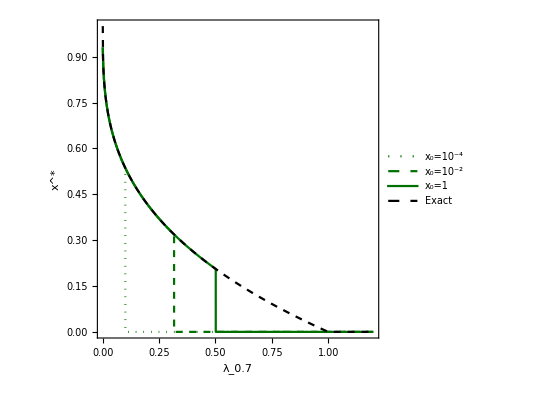

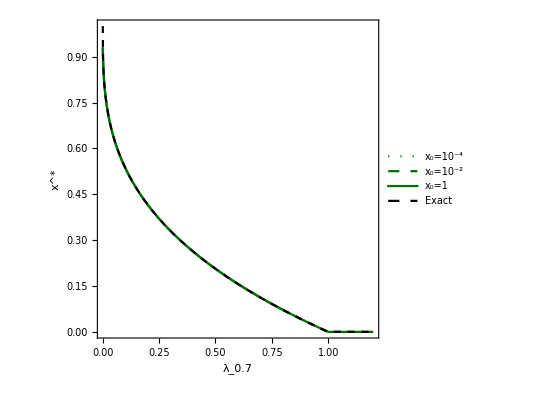

```mathematica
ListPlot[

x0 list,
Joined->True,
Frame->True,
AspectRatio->1,
PlotStyle->{{Green//Darker//Darker,Dotted},{Green//Darker//Darker,Dashed},{Green//Darker//Darker},{Dashed,Black}},

PlotLegends->Placed[{"x_0=10^-4","x_0=10^-2","x_0=1","Exact"},{Right,Top}],

FrameLabel->{"λ_0.7","x^*"},
FrameStyle->14
]
ListPlot[

x0 list lasso,
Joined->True,
Frame->True,
AspectRatio->1,
PlotStyle->{{Green//Darker//Darker,Dotted},{Green//Darker//Darker,Dashed},{Green//Darker//Darker},{Dashed,Black}},

PlotLegends->Placed[{"x_0=10^-4","x_0=10^-2","x_0=1","Exact"},{Right,Top}],

FrameLabel->{"λ_0.7","x^*"},
FrameStyle->14
]
```

```mathematica
x0 list lasso[[1]]
```

{{0.,0.84453},{0.0001,0.843707},{0.0002,0.842886},{0.0003,0.842069},{0.0004,0.841255},{0.0005,0.840444},{0.0006,0.839636},{0.0007,0.838832},{0.0008,0.83803},{0.0009,0.837232},{0.001,0.836437},{0.0011,0.835645},{0.0012,0.834856},{0.0013,0.83407},{0.0014,0.833288},{0.0015,0.832508},{0.0016,0.831731},11967,{1.1984,0},{1.1985,0},{1.1986,0},{1.1987,0},{1.1988,0},{1.1989,0},{1.199,0},{1.1991,0},{1.1992,0},{1.1993,0},{1.1994,0},{1.1995,0},{1.1996,0},{1.1997,0},{1.1998,0},{1.1999,0},{1.2,0}}
 |  |  |  |

```mathematica
?update
```

```mathematica
?lasso
```

```mathematica
X={0};
For[i=1,i<100,i++,
AppendTo[X,lasso[X[[-1]],0.8,0.5,4]]
]
```

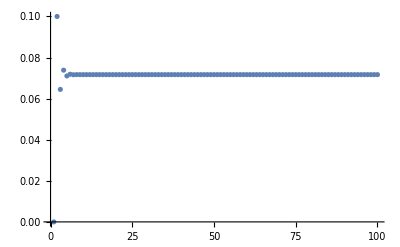

```mathematica
ListPlot[X]
```

```mathematica
lass
```